```mathematica
ClearAll["Global'*"]
LHS = Assuming[{c>R>0},∫_R^c p A ⅇ^(-(B p r^2)/(Eo c^2))ⅆr]
LHS = Normal[Simplify[Series[%,{c,∞,1}]]]
```

1/(2 √((B p)/Eo))A p √π (Erf[√((B p)/Eo)]-Erf[(√((B p)/Eo) R)/((2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True)]) ((2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True)

-A p R+(A p √π Erf[√((B p)/Eo)] ((2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True))/(2 √((B p)/Eo))

```mathematica
RHS = Log[Q];
Sol1 = Solve[LHS==RHS,c];
c = Normal[c/.Sol1[[1]]]
Normal[Simplify[Series[%,{p,0,1}]]]
Vc[R_] = R Eo(c/R)^2;
Sol2 = Solve[D[Vc[R], R]==0,R];
Vmin = Vc[R]/.Sol2[[2]];
Rmin = R/.Sol2[[2]];
Print["Vc[R] = ",Vc[R], " (V)"];
Print["Rmin = ",Rmin, " (m)"];
Print["Vmin = ",Vmin, " (V)"];
```

General::ivar: 2\ √B\ p/Eo\ (A\ p\ R + Log[Q])/A\ p\ √π\ Erf[√B\ p/Eo] is not a valid variable.

ReplaceAll::reps: {True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True

(2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True

ReplaceAll::reps: {True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ReplaceAll::reps: {True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{R → -2\ B\ Log[Q] + A\ Eo\ √« 1 »\ « 1 »\ Erf[« 1 »]\ « 1 »[0, True]/2\ A\ B\ p}} does not exist.

ReplaceAll::reps: {{{R → Times[« 3 »] + Times[« 6 »]/2\ A\ B\ p}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{R → -2\ B\ Log[Q] + A\ Eo\ √« 1 »\ « 1 »\ Erf[« 1 »]\ « 1 »[0, True]/2\ A\ B\ p}} does not exist.

ReplaceAll::reps: {{{R → Times[« 3 »] + Times[« 6 »]/2\ A\ B\ p}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

Part::partw: Part 2 of {{R → -2\ B\ Log[Q] + A\ Eo\ √« 1 »\ « 1 »\ Erf[« 1 »]\ « 1 »[0, True]/2\ A\ B\ p}} does not exist.

ReplaceAll::reps: {{{R → Times[« 3 »] + Times[« 6 »]/2\ A\ B\ p}} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Vc[R] = (Eo ((2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True)^2)/R (V)

Rmin = R/.{{R→1/(2 A B p)(-2 B Log[Q]+A Eo √((B p)/Eo) √π Erf[√((B p)/Eo)] InverseFunction[ReplaceAll,1,2][0,True])}}⟦2⟧ (m)

Vmin = (Eo ((2 √((B p)/Eo) (A p R+Log[Q]))/(A p √π Erf[√((B p)/Eo)])/.True)^2)/R/.{{R→1/(2 A B p)(-2 B Log[Q]+A Eo √((B p)/Eo) √π Erf[√((B p)/Eo)] InverseFunction[ReplaceAll,1,2][0,True])}}⟦2⟧ (V)

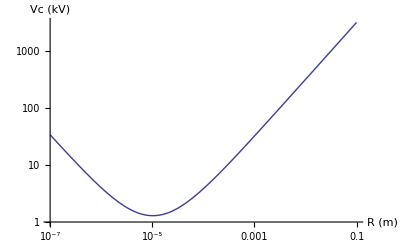

```mathematica
A = 8.85072785591;
B = 243.770046879;
Q = 10^4;
p= 101325;
Eo = 24.72 10^5;
LogLogPlot[Vc[R]/1000, {R,10^-7,10^-1}, AxesLabel-> {"R (m)", "Vc (kV)"}]
```